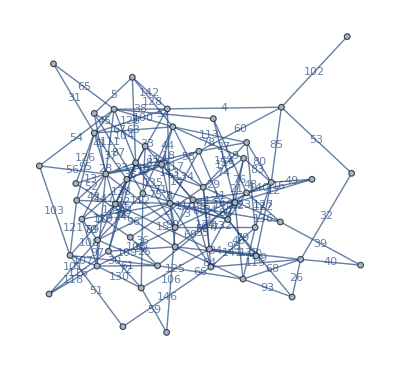

```mathematica
𝒢=GraphUnion@@ConnectedGraphComponents@RandomGraph[{54,148},EdgeWeight->RandomSample[Range[148]],EdgeLabels->"EdgeWeight"]
```

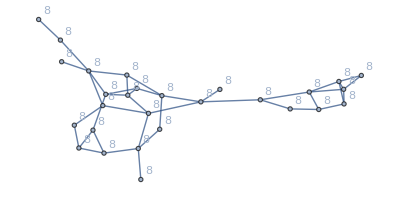

```mathematica
Subgraph[𝒢,Select[VertexList@𝒢,EvenQ[VertexDegree[𝒢,#]]&],VertexLabels->(VertexDegree[𝒢,#]&/@VertexList[𝒢]),EdgeLabels->None]
```

```mathematica
FindIndependentVertexSet[Subgraph[𝒢,Select[VertexList@𝒢,OddQ[VertexDegree[𝒢,#]]&],VertexLabels->(VertexDegree[𝒢,#]&/@VertexList[𝒢]),EdgeLabels->None]]
```

{{1,7,10,13,18,24,32,36,49,51,52,54}}

```mathematica
Partition[First[FindIndependentVertexSet[Subgraph[𝒢,Select[VertexList@𝒢,OddQ[VertexDegree[𝒢,#]]&],VertexLabels->(VertexDegree[𝒢,#]&/@VertexList[𝒢]),EdgeLabels->None]]],2]
```

{{1,7},{10,13},{18,24},{32,36},{49,51},{52,54}}

```mathematica
UndirectedEdge@@@Partition[First[FindIndependentVertexSet[Subgraph[𝒢,Select[VertexList@𝒢,OddQ[VertexDegree[𝒢,#]]&],VertexLabels->(VertexDegree[𝒢,#]&/@VertexList[𝒢]),EdgeLabels->None]]],2]
```

{1<->7,10<->13,18<->24,32<->36,49<->51,52<->54}

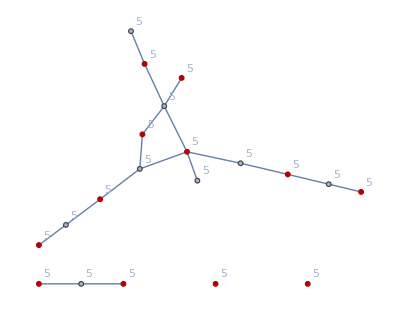

```mathematica
HighlightGraph[Graph[{1,7,10,13,14,18,19,24,28,30,32,34,36,37,42,46,49,51,52,54},{Null,SparseArray[Automatic,{20,20},0,{1,{{0,2,6,7,7,9,9,11,13,16,18,19,20,21,25,26,28,29,31,33,34},{{5},{7},{5},{9},{14},{15},{10},{1},{2},{1},{20},{12},{14},{2},{18},{19},{3},{17},{14},{8},{16},{2},{8},{11},{19},{2},{13},{18},{10},{9},{16},{9},{14},{7}}},Pattern}]},{VertexLabels->{5},EdgeWeight->{62,143,138,2,124,79,33,98,87,112,81,108,59,53,43,99,145}}],{{1,7,10,13,18,24,32,36,49,51,52,54}}]
```

```mathematica
Select[VertexList@𝒢,OddQ[VertexDegree[𝒢,#]]&]
```

{1,7,10,13,14,18,19,24,28,30,32,34,36,37,42,46,49,51,52,54}

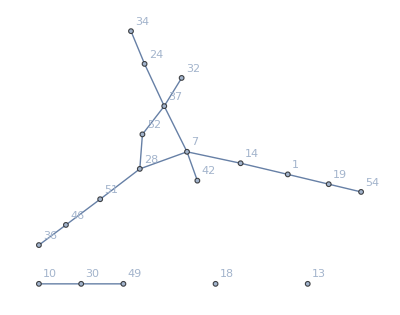

```mathematica
Graph[Fold[VertexDelete[#1,#2]&,𝒢,Complement[VertexList[𝒢],Select[VertexList@𝒢,OddQ[VertexDegree[𝒢,#]]&]]],VertexWeight->(VertexDegree[𝒢,#]&/@VertexList@Fold[VertexDelete[#1,#2]&,𝒢,Complement[VertexList[𝒢],Select[VertexList@𝒢,OddQ[VertexDegree[𝒢,#]]&]]]),VertexLabels->Automatic,EdgeLabels->None]
```